## Definitions

```mathematica
Cn[data_, n_]:=1./Sqrt[Length[data]] Sum[data[[x]]*Exp[2. Pi ⅈ n x/Length[data]],{x,1,Length[data]}]
fapprox[Cn_,x_,L_, $N_]:=1./Sqrt[L] Sum[Cn[n]Exp[2.ⅈ*n*π*x/L],{n,-$N,$N}];
fapprox[Cn_,x_, L_, $N_, Coeffs_]:=1./Sqrt[L] Sum[Cn[n]Exp[2.ⅈ*n*π*x/L],{n,Coeffs[[1;;$N]]}];
DiscreteApprox[n_]:= With[{approx = fapprox[x, Length[rlist], n]},{Length@approx, Table[Re@approx, {x,1,Length[rlist]}]}];
```

```mathematica
Options[FFTShift] = {k->All, Indices ->False};
```

```mathematica
FFTShift[dat_?ArrayQ,OptionsPattern[]]:=Module[{dims=Dimensions[dat], fftshifted, index},
fftshifted = RotateRight[dat,If[OptionValue[k]===All,Quotient[dims,2],Quotient[dims[[OptionValue[k]]],2] UnitVector[Length[dims],OptionValue[k]]]];
index = Table[n,{n,-Floor[dims[[1]]/2],If[EvenQ[dims[[1]]], Floor[ dims[[1]]/2]-1, Floor[dims[[1]]/2]]}];
If[OptionValue[Indices], Transpose[{index, fftshifted}], fftshifted]]
```

## Data

```mathematica
pointsraw = "366.1608769989015,61.74305137634278
366.4345677292348,62.69531416535378
366.71188702449206,63.66020196124911
366.9871484375,64.6179296875
367.2668360805511,65.59105776786805
367.70166503906256,65.56147949218749
367.97617837056515,64.60635459497571
368.25164489746095,63.64791320800782
368.5314617824555,62.6743354511261
368.80562874436384,61.72362472772599
369.13356099249796,60.769596705920996
369.4548920799978,59.83477293211968
369.779265504647,58.89109832126647
370.10786243686454,57.93513658527285
370.43367369771005,56.98727898836136
370.75828157642854,56.042922298349445
371.0815594169101,55.102434986098665
371.4062201349996,54.15792457457632
371.72868778675564,53.2197942819586
372.0545757433982,52.27171355987433
372.38195895388725,51.31928281098604
372.7090964794159,50.36756681442261
373.03442081717077,49.42112578534056
373.35652751263933,48.48404559503775
373.6838599869446,47.53176244901959
374.0058465731144,46.59503168344498
374.3313525095373,45.64806234335061
374.6596864952706,44.692865577302875
374.98011823942886,43.76065819378942
375.30696472481446,42.80978889788909
375.634573154666,41.85670293566305
375.9572440236737,40.917981438753195
376.2844088846238,39.96618591735431
376.61036479368806,39.01790750652552
376.93445139899586,38.075067317082436
377.25600834867686,37.13958645984065
377.58411352103434,36.1850553629169
377.9081061553955,35.2424885559082
378.23198628006503,34.300249064676464
378.5593917150866,33.347753659668385
378.88441725238664,32.40218190772633
379.21028661097165,31.454155291537752
379.5310683466308,30.52092970471829
379.8577102349489,29.570655627301896
380.18324276458617,28.62360892161785
380.50849186971783,27.677386761009693
380.8329968942492,26.73332929675933
381.16108013903715,25.778861992023884
381.48374272674556,24.840164587260226
381.8100507725775,23.890861732065677
382.13514843741433,22.945080145038666
382.45915916487576,22.002460701167585
383.2350236129761,21.68
384.2241793823242,21.68
385.2325016719103,21.68
386.2301931434125,21.68
387.2199246388674,21.68
388.2386157226563,21.68
389.2190831375122,21.68
390.234616394043,21.68
390.07068673355735,22.48562258287333
389.72214856779203,23.42373742379248
389.3740429551713,24.36068801768124
389.02395261911676,25.302980633452535
388.6810105419159,26.226033210754395
388.32922293428885,27.172894151626387
387.9804511384666,28.11163782417774
387.63630298053846,29.037936652079225
387.28556236878734,29.981979530351236
386.93632818928484,30.921967740905238
386.5855731563666,31.86604943475686
386.24128837527707,32.79271599344909
385.8933666609324,33.729171612270875
385.5429313422859,34.672392772807505
385.19749437953084,35.60216050900635
384.845228338888,36.550309185789665
384.5000632883262,37.47934505130979
384.1495571628041,38.42275679350249
383.8010729796998,39.360726336315274
383.45533107553376,40.291314843641594
383.10597422242165,41.23163323879242
382.7605140104136,42.16146355198114
382.40883987852754,43.10801906496272
382.0620519795871,44.041422940354096
381.7098641227372,44.98936117999256
381.3634759371914,45.92168919883669
381.0160994488187,46.85667730383575
380.66811722645537,47.7932957842201
380.3199118389376,48.73051492922008
379.9718658551015,49.66730502806604
379.62436184378345,50.60263636998832
379.2777823738195,51.53547924421728
378.9253334796036,52.48412008417654
378.57465370680904,53.42799921014346
378.2296938438772,54.35648279881207
377.8802294494211,55.29709064900875
377.53033433214057,56.2388578198012
377.1839849781803,57.17108132071793
376.8348099212544,58.11091039872379
376.4902326331404,59.03836426052265
376.13750684997854,59.98775036643841
375.7907570963166,60.921051571145654
375.44414412667277,61.853984612105414
375.0923933540494,62.80074640898965
374.74908256358697,63.724791403813285
374.39717935946334,64.67196348073776
374.0503440341368,65.60549500756315
373.69895339056853,66.5512874919176
373.3562732593715,67.47363502323628
373.0089635950886,68.40844326652586
372.65658419091517,69.35689706917736
372.3093153063697,70.29159555095248
371.96089347854024,71.22939726018348
371.6110848894157,72.17093153439463
371.26504838824275,73.10231297016144
370.91648687463487,74.04049065343105
370.56809770703313,74.97820445537567
369.57917609855537,75
368.58442635223264,75
367.57378867030144,75
366.5872482149303,75
365.5781888206303,75
364.5759523773193,75
364.09749848356466,74.26654311679303
363.7444074469991,73.31617390580476
363.40111228326333,72.39217097140848
363.05102131819615,71.44987666260567
362.7023403982699,70.51137758888187
362.35229497118155,69.56920584873296
362.0050370779258,68.63453695078265
361.6570411412418,67.6978815573454
361.3072694880167,66.75644669868983
360.9645395939052,65.83396522700787
360.6147710615283,64.89253876833362
360.26535519480706,63.95206153392792
359.9180782559016,63.017341373279926
359.56823262018065,62.075707385564456
359.2168695078791,61.12998900353908
358.8715443208444,60.200522119506495
358.52012649885614,59.25465648253448
358.17669772672264,58.330293931794586
357.8285632146895,57.3932655531168
357.47618183987885,56.4448064463574
357.12702968973696,55.50503902356257
356.78174491517944,54.5756809125375
356.4337856941539,53.63912434186204
356.0835590076447,52.69646472930908
355.7386732017994,51.76818047046662
355.38877143815847,50.82639541053053
355.0378321949803,49.88181790188537
354.68987662292,48.9452711526549
354.34167397515296,48.00805938188569
353.9936068205154,47.0712123003474
353.6460577278436,46.13575961880968
353.29940926597374,45.20273104804219
352.95404400374184,44.27315629881457
352.60320455744164,43.32884740044363
352.25450799060957,42.390306211978896
351.9083612842299,41.45862815119326
351.5582011860027,40.51614776565693
351.2115522582829,39.58311794102192
350.8620359986063,38.64237049195799
350.5103663922529,37.69582715976401
350.16392561410066,36.76335758424247
349.81670687183737,35.82879406392574
349.469576089296,34.894467293350026
349.1172457071743,33.94614543697797
348.773311913989,33.02042358676903
348.42659459397197,32.08720967948437
348.0731054246871,31.135768866447037
347.7263432850686,30.202434324071508
347.3772518539615,29.262830330803986
347.02889588162304,28.325205876231195
346.68001701354984,27.386174011230466
346.33543920366094,26.458718745037913
345.9846863460541,25.514642906188964
345.63913986360654,24.58458039008081
345.2885424245894,23.640922871232032
344.9380417716503,22.69752585887909
344.5921357822418,21.76649570465088
345.4582005596161,21.68
346.47543348506093,21.68
347.4756029987335,21.68
348.47499999999997,21.68
349.4743970012665,21.68
350.47456651493906,21.68
351.4610482895374,21.68
352.4123376941681,21.744985332489012
352.7372708487324,22.69028832245618
353.0634772266261,23.63929540295154
353.39139631701636,24.593285145945845
353.7165752591356,25.53930318670813
354.0373063259386,26.47238136652857
354.36290526747706,27.419621279239653
354.6909109768763,28.373863016242975
355.0165048199493,29.32108809638128
355.34401047095656,30.273875052034857
355.6663944044025,31.211761789423765
355.989919171799,32.15296746712178
356.317501290571,33.105976884551346
356.64321006913434,34.05353633765597
356.96564509263493,34.99157170740422
357.2932614202588,35.944680646010674
357.6154809792898,36.88208918157965
357.94117799154714,37.82961440387647
358.2646667635048,38.77071536281786
358.59019754663115,39.71775698751212
358.91710998905563,40.66881816714361
359.2447437389078,41.621977790896786
359.56739983430833,42.56065630808938
359.8894846835616,43.49767294288147
360.2153688526238,44.44574264605006
360.53935324015094,45.38828546117991
360.8656990215205,46.33769809746649
361.1935789685042,47.291573963564005
361.51730320123954,48.23335993040353
361.84086677059537,49.17467849165202
362.1678998837829,50.12609072943684
362.49249963629615,51.07042377850565
362.8178806627193,52.01702972756233
363.14237189109645,52.961047055724194
363.46822088828105,53.909014436059515
363.79285261020067,54.8534404912591
364.1207799626538,55.80745427043643
364.4438618732989,56.74737157911062
364.7702626004326,57.69694406487513
365.09094933358955,58.62989326823503
365.4196649932862,59.58620040893555
365.74037258839235,60.51921030435712
366.06842705221845,61.47359387885779";
Iconize[pointsraw]
```

```mathematica
points = ToExpression[StringJoin["{{",StringReplace[pointsraw, "\n"->"},{"],"}}"]];
points = {#[[1]],-#[[2]]}&/@points;
pointscentered =(#-Mean@points)&/@points;
pointsShifted = MapAt[(#+25)&,pointscentered, {All,2}];
```

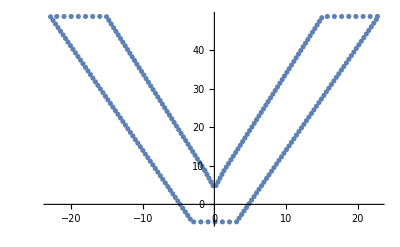

```mathematica
ListPlot[pointsShifted]
```

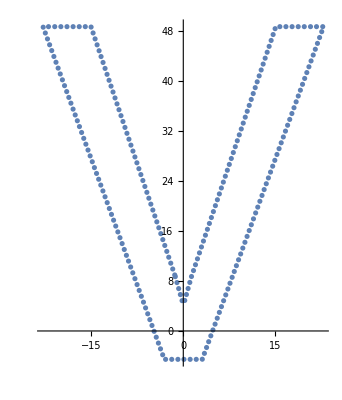

```mathematica
ListPolarPlot[(Reverse@*ToPolarCoordinates/@pointsShifted)]
```

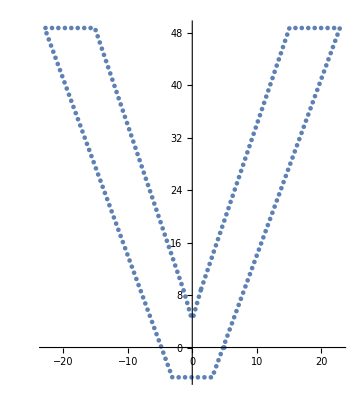
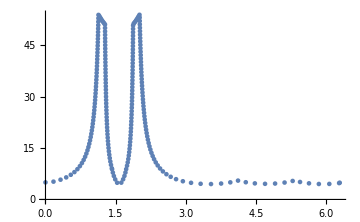

```mathematica
polarpoints = SortBy[MapAt[Abs[#-Pi]&,(Reverse@*ToPolarCoordinates/@pointsShifted),{All,1}], First];
PrependTo[polarpoints,{0,Mean[{polarpoints[[1,2]],polarpoints[[-1,2]]}]}];
AppendTo[polarpoints,{2Pi,Mean[{polarpoints[[1,2]],polarpoints[[-1,2]]}]}];
Row[#[polarpoints, ImageSize->Medium,PlotRange->Full]&/@{ListPolarPlot,ListPlot}]
```

```mathematica
ppointsFunc = Interpolation[polarpoints,InterpolationOrder->1];
```

```mathematica
ppointSample = ppointsFunc[Subdivide[0,2π,2^9-1]]; (*Take even sample of 512 points*)
ppointSample[[1]]=ppointSample[[-1]] = Mean[{ppointSample[[1]],ppointSample[[-1]]}];
```

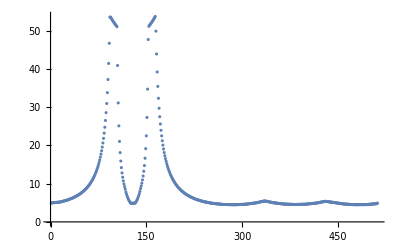

```mathematica
ListPlot[ppointSample,PlotRange->All]
```

## Using FFT

```mathematica
fftcoefs = Fourier[ppointSample];
fftshifted = FFTShift[fftcoefs, Indices->True];
FFTCoeff[n_]:=Conjugate[Last@SelectFirst[fftshifted, #[[1]]==n&]]; (*Applied Conjugate to coefficients because the time series was reversed*)
```

```mathematica
invfft[n_]:=fapprox[FFTCoeff, x*Length@ppointSample/(2π), Length@ppointSample, n]
```

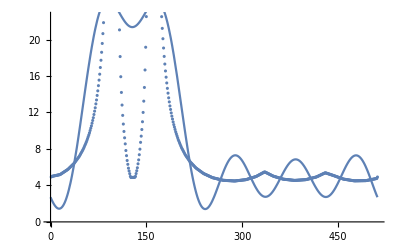

```mathematica
Show[{ListPlot[ppointSample], Plot[Re@invfft[10], {x,0,2π}]}]
```

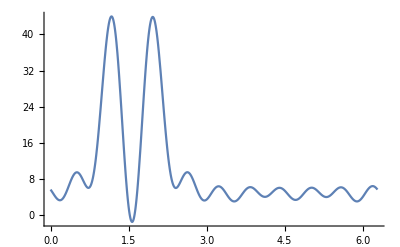

```mathematica
Plot[Re@invfft[10], {x,0,2π},PlotRange->All]
```

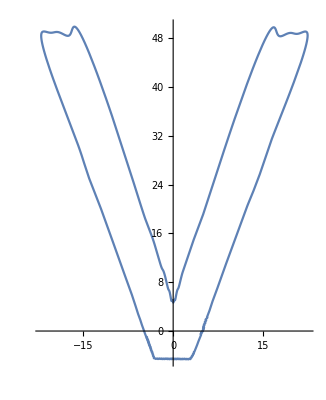

```mathematica
PolarPlot[Re@invfft[ x*Length@ppointSample/(2π)],{x,0,2Pi},PlotRange->Full]
```

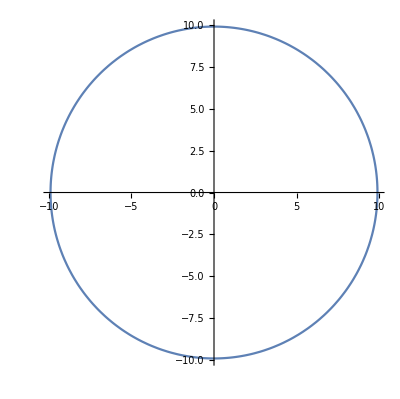
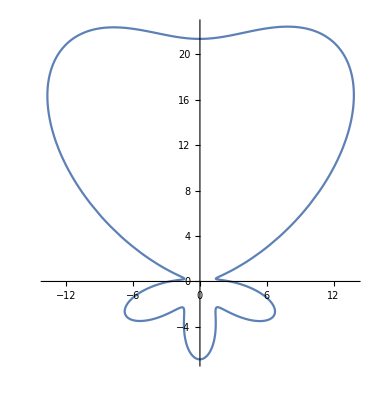
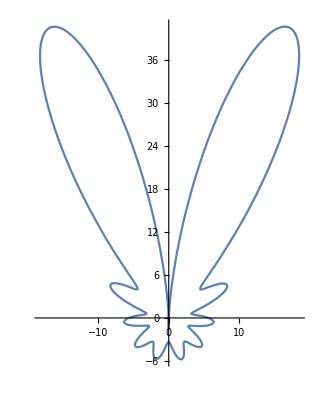
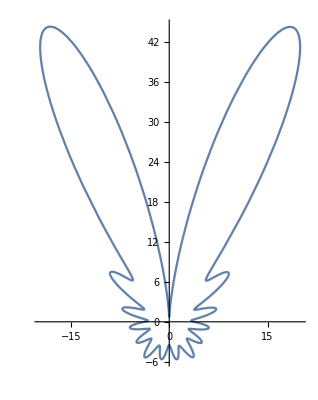
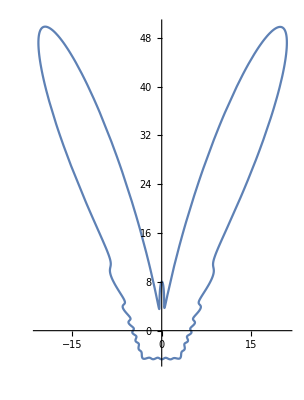
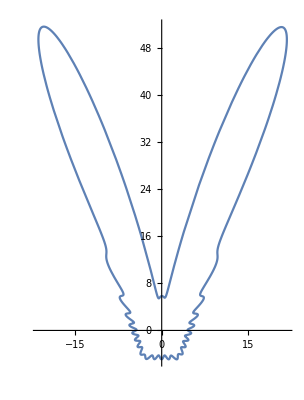
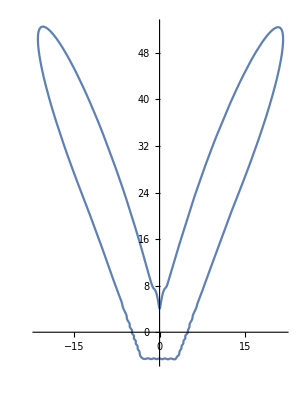
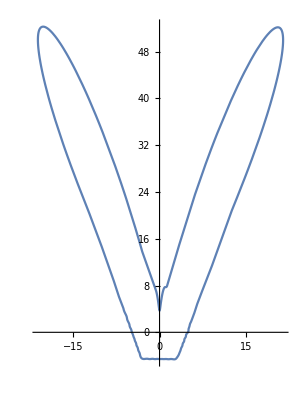

```mathematica
Table[With[{f=invfft[n]},PolarPlot[Re@f,{x,0,2Pi},PlotRange->Full]],{n,0,50,5}]
```